# 1.1.3 2D Plotting Guide: Plot[ ] and Plot Options part 1

## Plotting a function

Learning to plot functions is one of the most essential skills one can learn with Wolfram Mathematica. Though this guide gives an extensive overview of what can be done with the Plot[ ] function, but it is not exhaustive! If there is something you would like to learn more about, simply search for it on the Wolfram Documentation page: https://reference.wolfram.com/language/

To plot a function, use the Plot[ ] function as shown in the example below. The essential arguments of the Plot[ ] function are a function to plot (Sin[x^2] + x in this example), and a range for the independent variable ({x, -4, 4}). 

Note: Do not forget that Mathematica is very sensitive to syntax. Capitol letters are for Mathematica's built-in function, brackets are for function inputs, and braces are for lists, arrays, and points.

#### Example: Simple Plot[ ]

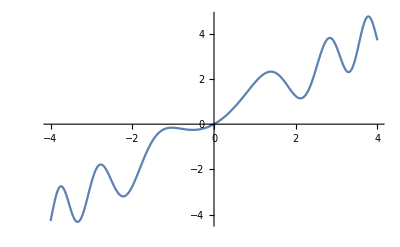

```mathematica
Plot[Sin[x^2]+x,{x,-4,4}]
```

The Plot[ ] function has many options to make your plots more useful and look better. We will discuss some here.

#### Exercise 1: Define the function d[x] as Cos[x]/(x^2+1), and plot d[x] from -3Pi to 3Pi.

## Framing Options: Plot Range, Aspect Ratio, & Labelling

For simplicity, we name our desired function f[x].

```mathematica
f[x_]:=Sin[x^2]+x;
```

### PlotRange

We can specify the window dimensions of a plot with PlotRange -> { {x-coordinates}, {y-coordinates}}. This is particularly helpful when needing a specific y-coordinate in view.

#### Example: Plot with PlotRange

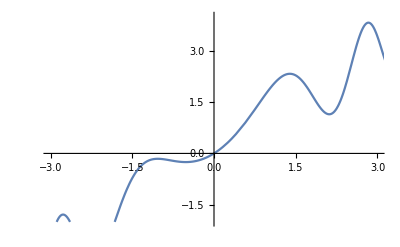

```mathematica
Plot[f[x],{x,-4,4},PlotRange->{{-3,3},{-2,4}}]
```

### AspectRatio

Often times, we will want to change the aspect ratio (or its rectangular area). We do this with AspectRatio -> Ratio of y-direction over x-direction. For example, AspectRatio -> 1 frames the plot in a square. In the plot below, AspectRatio -> 4/5 frames the plot in a rectangle 4 units height and 5 units wides.

#### Example: Plot with AspectRatio

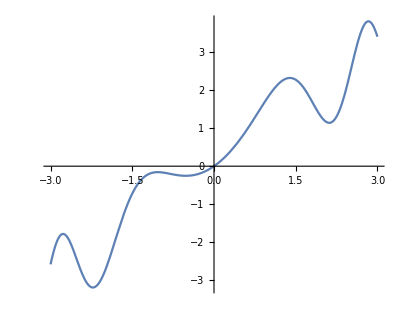

```mathematica
Plot[f[x],{x,-3,3},AspectRatio->4/5]
```

### Combining Options

Mathematica makes it easy to combine options simply by placing them each within the Plot[ ] function.

#### Example: PlotRange and AspectRatio

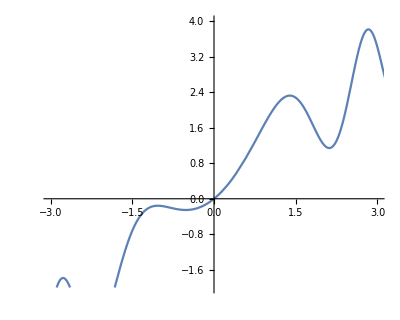

```mathematica
Plot[f[x],{x,-4,4},PlotRange->{{-3,3},{-2,4}},AspectRatio->4/5]
```

#### Exercise 2: Plot d[x] from Example 1 on a specified plot range and aspect ratio of your choice.

## Graphic Options: PlotStyle, Filling, and Background

### PlotStyle

With PlotStyle, we can change the plot's color and thickness. Note that we will still be using PlotRange and AspectRatio in the following examples.

#### Example: Changing the Color with PlotStyle

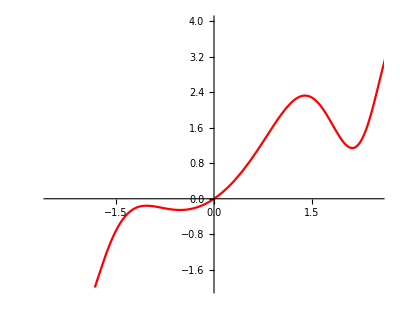

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,4}},AspectRatio->4/5, PlotStyle ->Red]
```

#### Exercise 3: Plot a nonlinear function and change the color. Be sure to change the plot range and the aspect ratio.

With CMYKColor and RGBColor functions, we can specify colors by their CMYK or RGB code.

#### Example: Changing the Color Using CMYKColor and RGBColor

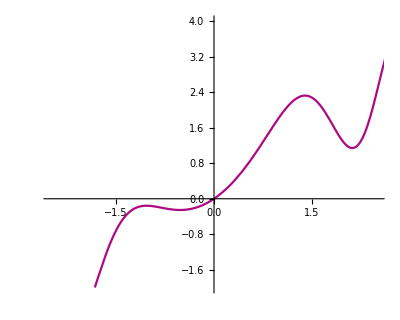

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,4}},AspectRatio->4/5, PlotStyle -> CMYKColor[0.2, .95, 0.4, .15]]
```

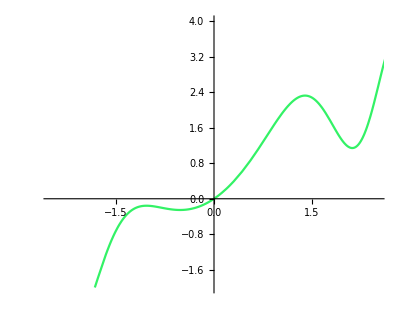

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,4}},AspectRatio->4/5,PlotStyle -> RGBColor[.2,.95,.4]]
```

#### Exercise 4: Change the color of your function using either CMYKColor or RGBColor.

Note in the example below, we change the plot to be blue, slightly thicker than normal, and dashed. We can specify multiple characteristics with Directive[ ].

#### Example: Using Directive to Add Multiple PlotStyle Options

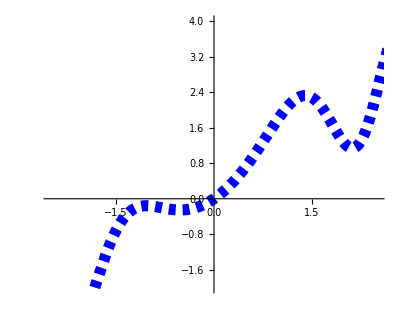

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,4}},AspectRatio->4/5, PlotStyle -> Directive[Blue,Thickness[0.02],Dashed]]
```

#### Exercise 5: Plot a nonlinear function and use Directive to change at least two aspects of the plot (color, thickness, dashed, etc.) Note: Line thickness is very sensitive. A few hundredths is recommended.

### Filling and FillingStyle

It is not uncommon to want to have plots with shading. We accomplish this with Filling.

#### Example: Using Filling -> Bottom to shade underneath

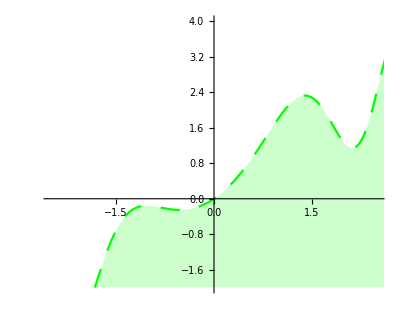

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,4}},AspectRatio->4/5, PlotStyle -> Directive[Green,Dashing[Large]],Filling->Bottom]
```

Different Fillings have different applications. the figure below displays Top, Bottom, Axis, and a specified horizontal line.

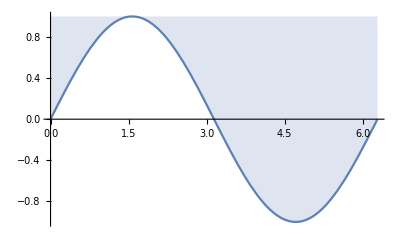
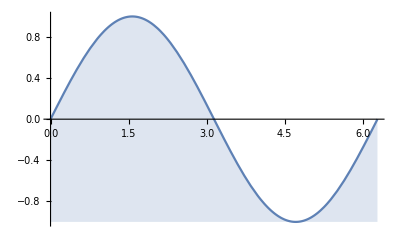
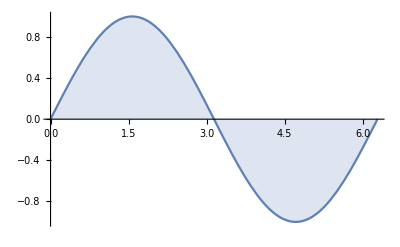
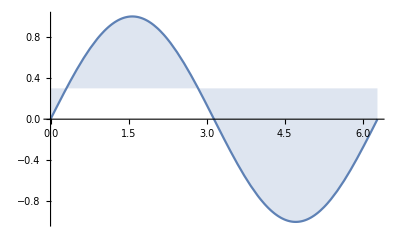

```mathematica
Table[Plot[Sin[x], {x, 0, 2 Pi}, 
  Filling -> f], {f, {Top, Bottom, Axis, 0.3}}]
```

Our plot's color defaults to that specified by PlotStyle, but FillingStyle allows us to change the filling. Similarly, using ColorFunction instead of PlotStyle allows for gradient fillings.

#### Example: Using FillingStyle

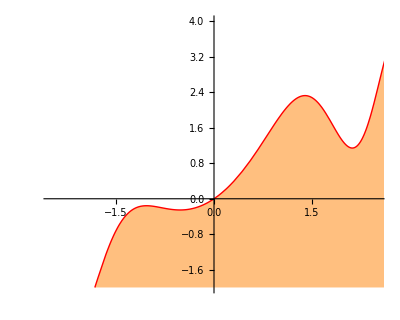

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,4}},AspectRatio->4/5, PlotStyle -> Directive[Red,Thick],Filling->Bottom,FillingStyle->Directive[Orange,Opacity[0.5]]]
```

#### Example: Using FillingStyle

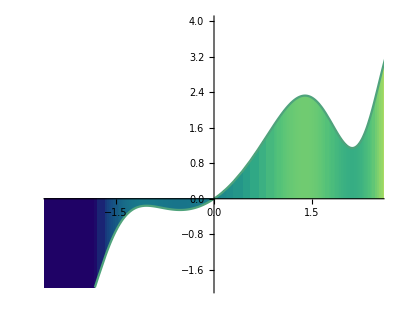

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,4}},AspectRatio->4/5, ColorFunction->"BlueGreenYellow",Filling->Axis]
```

#### Exercise 6: Plot a nonlinear function with filling to the axis. Use PlotStyle, FilingStyle, and Directive to change the plot's asthetic. Be sure to change the plot range and the aspect ratio as needed.

### Background

Like PlotStyle and FillingStyle, Background specifies the color of the the plot's background.

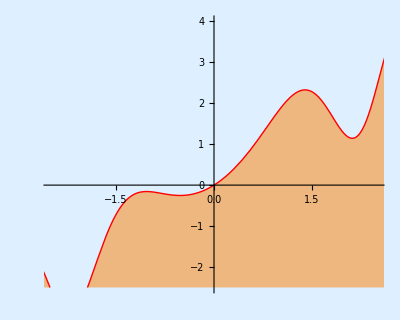

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2.5,4}},AspectRatio->4/5, PlotStyle -> Directive[Red,Thick],Filling->Bottom,FillingStyle->Directive[Orange,Opacity[0.5]],Background->LightBlue]
```

### PlotLabel

We can label our plots with PlotLabel. In the example below, we label the plot by specifying the function name, framed, in blue with font size 17.

#### Example: Labelling a plot with PlotLabel

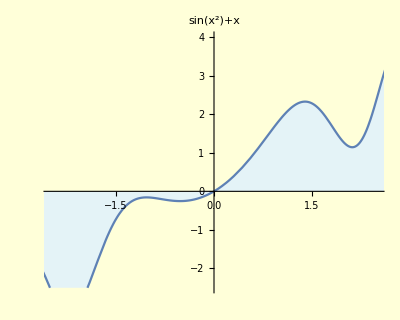

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2.5,4}},AspectRatio->4/5,PlotLabel->Style[Framed[f[x]],17,Blue],Filling->Axis,FillingStyle->Directive[LightBlue,Opacity[.8]],Background->LightYellow]
```

#### Exercise 7: Plot a nonlinear function with a LightBlue background. Use PlotLabel -> f[x] to add a label. Use material from previous exercises to add filling, change colors, and adjust aspect ratio.

## Plotting Multiple Functions

Plotting multiple functions is a simple task in Mathematica. In the Plot[ ] function, we simply list the functions we desire to plot. Let us define a second function.

```mathematica
g[x_]:=1+2x*Cos[x^2];
```

#### Example: Plotting f[x] and g[x] together

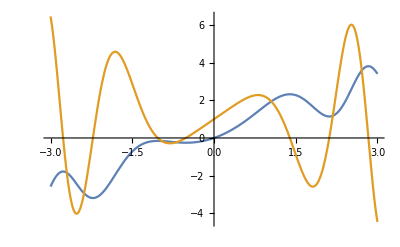

```mathematica
Plot[{f[x],g[x]},{x,-3,3}]
```

#### Exercise 8: Define and plot two nonlinear functions.

The example below demonstrates how to change PlotStyle when dealing with multiple functions. We simply add a list: PlotStyle -> {first plot attributes, second plot attributes}.

#### Example: Plotting f[x] and g[x] with specified attributes

Filling::invfillentry: {Charting`CommonDump`getRule[{}, 1]} is not a valid Filling specification.

Filling::invfillentry: {Charting`CommonDump`getRule[{}, 2], Charting`CommonDump`getRule[{}, 2]} is not a valid Filling specification.

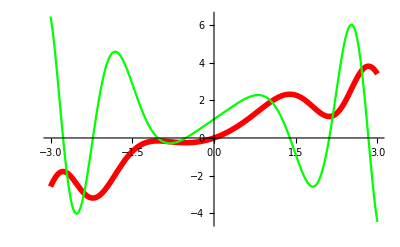

```mathematica
Plot[{f[x],g[x]},{x,-3,3},PlotStyle->{Directive[Red,Thickness[0.01]],Green},Filling->{{1->Bottom},{2->Top}},Background->Directive[LightBlue,Opacity[0.5]]]
```

#### Exercise 9: Plot the two functions from Example 8, but add PlotStyle, Filling, and Background.

### PlotLegends

It is not always clear which plot works with each function. Create a plot legend with PlotLegends.

#### Example: Creating a plot legend

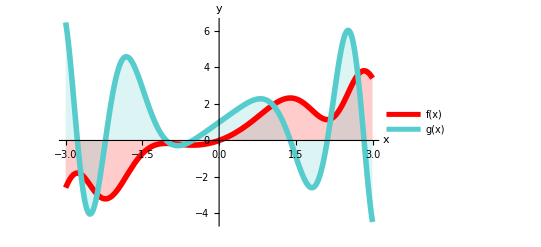

```mathematica
Plot[{f[x],g[x]},{x,-3,3},PlotStyle->{Directive[Red,Thickness[0.01]],Directive[RGBColor[.34,.8,.8],Thickness[0.01]]},Filling->Axis,PlotLegends->Placed["Expressions",Above],AxesLabel->{"x","y"}]
```

### Filling between curves and plotting with Table[ ]

In the example below, we using Filling to shade between two curves.

#### Example: Filling between two curves

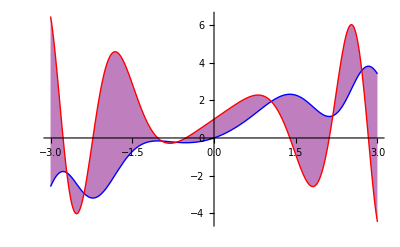

```mathematica
Plot[{f[x],g[x]}, {x, -3,3},PlotStyle->{Directive[Blue,Thick],Directive[Red,Thick]},Filling -> {1 -> {2}},FillingStyle->Directive[Purple,Opacity[0.5]]]
```

#### Exercise 10: Plot the two functions from Example 8, but create a plot legend and add filling between the curves.

In the example below, we plot a family of functions using Plot[Table[ ]]. To make it more colorful, we insert the Evaluate[ ] function. Notice, we also added a frame and changed the frame's style.

#### Example: Plotting a family of curves with Evaluate[Table[ ]]

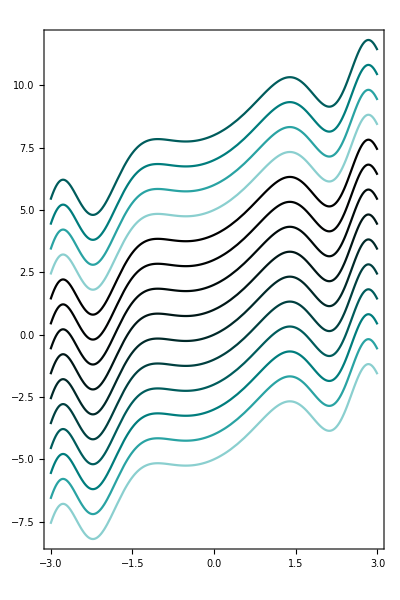

```mathematica
Plot[Evaluate[Table[f[x]+n, {n, -5,8}]],{x,-3,3},AspectRatio->3/2, PlotStyle-> Table[CMYKColor[.4k,.1k,.1k,.1k],{k,1,10}],Frame->True,FrameStyle->CMYKColor[.4,.1,.1,.1]]
```

## Resources

Wolfram’s Documentation Center: https://reference.wolfram.com/language/ref/Plot.html